# Mesh

## Topics

### Use Mesh to draw intersections of curves

References: http://mathematica.stackexchange.com/questions/10472/marking-points-of-intersection-between-two-curves

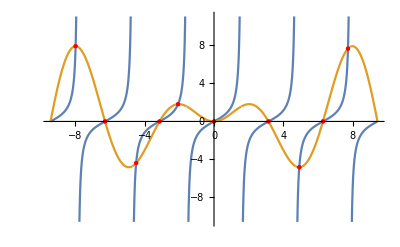

```mathematica
points=NSolve[Tan[x]==x Sin[x]&&-3 Pi<x<3 Pi,x][[All,1,2]];
Plot[{Tan[x],x Sin[x]},{x,-3 Pi,3 Pi},Mesh->{points},MeshStyle->{Directive[Red,PointSize[Large]]},Exclusions->Range[-5 Pi/2,5 Pi/2,Pi]]
```

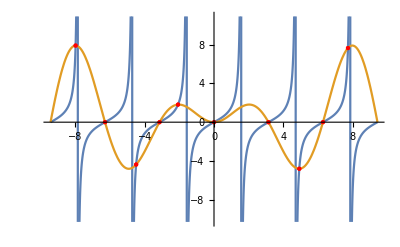

```mathematica
points=NSolve[Tan[x]==x Sin[x]&&-3 Pi<x<3 Pi,x][[All,1,2]];
Plot[{Tan[x],x Sin[x]},{x,-3 Pi,3 Pi},Mesh->{points},MeshStyle->{Directive[Red,PointSize[Large]]}]
```

#### Use MeshFunction

```mathematica
Plot[{Tan[x],x Sin[x]},{x,-3 Pi,3 Pi},Exclusions->Range[-5 Pi/2,5 Pi/2,Pi],MeshFunctions->{(Tan[#]-# Sin[#])&},Mesh->{{0}},MeshStyle->Directive[Red,PointSize[Large]]]
```

-Graphics-